7/16-x^3+(-1/4+x^2)^2

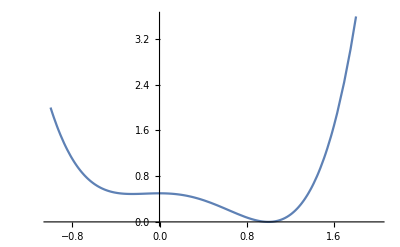

1.69857

{{x→-1/4},{x→0},{x→1}}

```mathematica
action=(x^2-1/4)^2 -x^3+7/16
Plot[action, {x,-1,2}]
N[Integrate[Exp[-action], {x,-∞,∞}]]
xsol=Solve[D[action,x]==0,x]
```

```mathematica
Do[tmp=xsol[[i]]; Print[Style[tmp,Red]];
Print[action/.tmp]; Print[D[action,x]/.tmp]; Print[D[action,{x,2}]/.tmp],
{i,3}]
```

{x→-1/4}

125/256

0

5/4

{x→0}

1/2

0

-1

{x→1}

0

0

5

```mathematica
tsol=Solve[action==t,x];
```

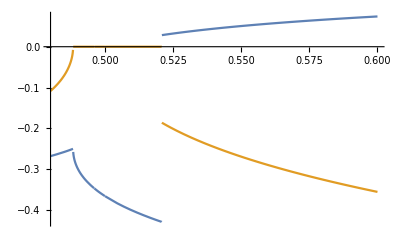

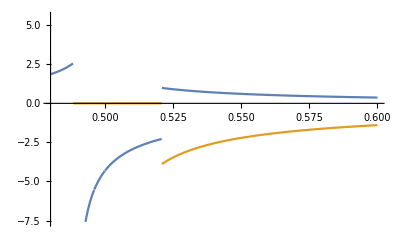

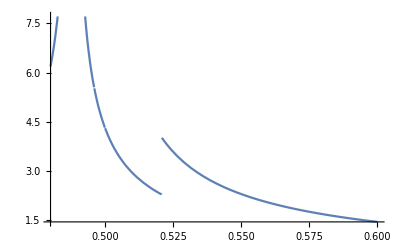

```mathematica
x1=x/.tsol[[1]];
Plot[{Re[x1], Im[x1]}, {t,0.48,0.6}]
ds1=D[action,x]/.x->x1;
Plot[{Re[1/ds1], Im[1/ds1]}, {t,0.48,0.6}]
Plot[{Abs[1/ds1]}, {t,0.48,0.6}]
```

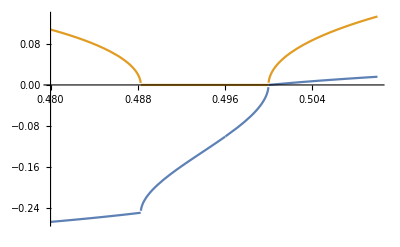

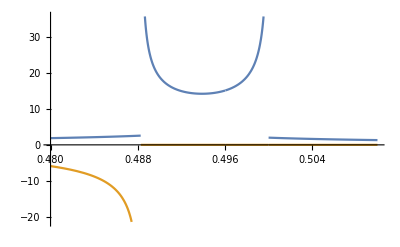

```mathematica
x2=x/.tsol[[2]];
Plot[{Re[x2], Im[x2]}, {t,0.48,0.51}]
ds2=D[action,x]/.x->x2;
Plot[{Re[1/ds2], Im[1/ds2]}, {t,0.48,0.51}]
```

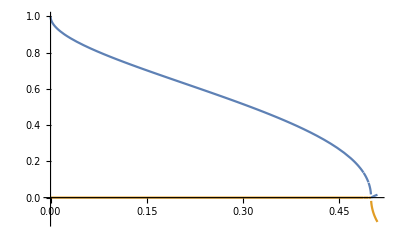

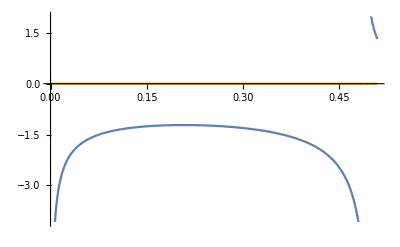

```mathematica
x3=x/.tsol[[3]];
Plot[{Re[x3], Im[x3]}, {t,0,0.51}]
ds3=D[action,x]/.x->x3;
Plot[{Re[1/ds3], Im[1/ds3]}, {t,0,0.51}]
```

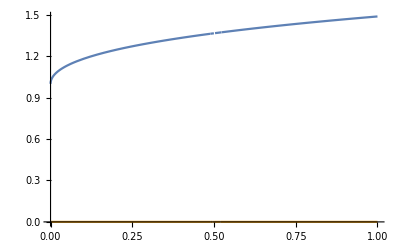

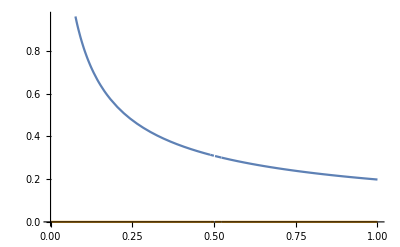

```mathematica
x4=x/.tsol[[4]];
Plot[{Re[x4], Im[x4]}, {t,0,1}]
ds4=D[action,x]/.x->x4;
Plot[{Re[1/ds4], Im[1/ds4]}, {t,0,1}]
```

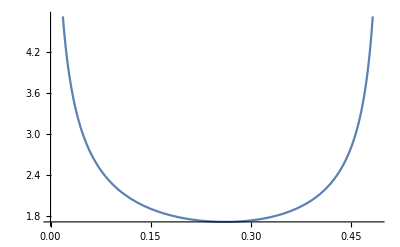

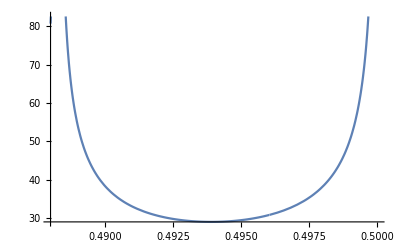

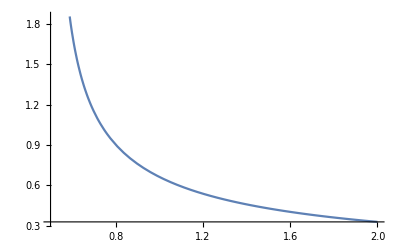

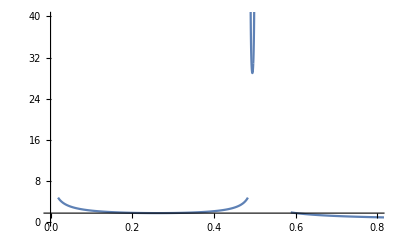

```mathematica
Plot[Abs[1/ds3]+Abs[1/ds4], {t,0,0.49}]
Plot[Abs[1/ds1]+Abs[1/ds2]+Abs[1/ds3]+Abs[1/ds4], {t,0.488,0.5}]
Plot[Abs[1/ds1]+Abs[1/ds4], {t,0.5,2}]
Show[%%%,%%,%, PlotRange->{{0,0.8}, {0,40}}]
```

```mathematica
N[(Abs[1/ds3]+Abs[1/ds4]) /. t->5^3/2^8]
N[(Abs[1/ds3]+Abs[1/ds4]) /. t->1/2]
```

5.74814

N::meprec: Internal precision limit $MaxExtraPrecision = 50. reached while evaluating -3 (1/4+(√3)/4-1/2 √(1+Times[«2»]))^2+4 (1/4+(√3)/4-1/2 √(1+1/2 Power[«2»])) (-1/4+(1/4+(√3)/4-1/2 √Plus[«2»])^2).

5.5031×10^16

```mathematica
NIntegrate[(Abs[1/ds3]+Abs[1/ds4])ⅇ^-t, {t,0,5^3/2^8}]
NIntegrate[(Abs[1/ds1]+Abs[1/ds2]+Abs[1/ds3]+Abs[1/ds4])ⅇ^-t, {t,5^3/2^8,1/2}]
NIntegrate[(Abs[1/ds1]+Abs[1/ds4])ⅇ^-t, {t,1/2,∞}](*!!!branch cut!!!*)
%%%+%%(*+%*)
```

0.996728

0.309468

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in t near {t} = {0.522019}. NIntegrate obtained 0.482472 and 0.00014791 for the integral and error estimates.

0.482472

1.3062

```mathematica
N[x1/.t->1/2]
N[x4/.t->1/2]
```

-0.366025+8.01234×10^-18 ⅈ

1.36603+2.1469×10^-18 ⅈ

```mathematica
N[Integrate[Exp[-action], {x,-0.3660254037844388,1.3660254037844388}]]
```

1.3062